# Laboratory 2 Functions, Dilations, Translations and Symmetry

Henry Osei

## Experiment 2.1

Plot each of the following functions using AspectRatio->Automatic, then plot the dilations (i.e., c f(x)) for the c values c=-.3, c=.8, c=1.5.

	1. y=x^2, on the interval [-3,3].
	
	2. y=sin x,  on the interval [0,3].
	
	3. y=e^x, on the interval [-2,1].  (Recall that E is Mathematica's notation for the constant  e =  2.7182...).
	
	4. y=√x, on the interval [0,3].
	
	5. y=cos x, on the interval [0,3].
	
	6. y = |x|, on the interval [-2, 2].
	
	What conclusions can you draw about the effect of multiplying f(x) by different constants? Your answer should contain a statement summarizing these different effects.

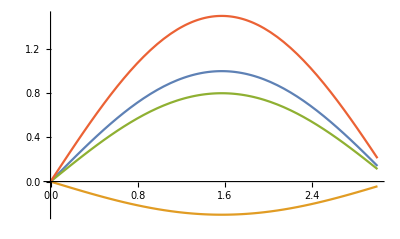

```mathematica
Clear[f]
f[x_] := Sin[x]
Plot[{f[x],-.3*f[x],.8*f[x],1.5*f[x]}, {x, 0, 3}, AspectRatio -> Automatic]
```

```mathematica
Clear[f]
f[x_] := Sqrt[x]
```

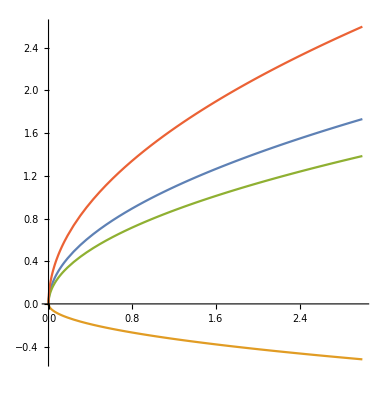

```mathematica
Plot[{f[x],-.3*f[x],.8*f[x],1.5*f[x]}, {x, 0, 3}, AspectRatio -> Automatic]
```

The effect of multiplying f(x) by a negative number flips it around the x-axis. Multiplying by a positive number less than 1 shrinks the graph in the y direction and multiplying by a positive number greater than 1 enlarges the  graph in the y direction.

## Experiment 2.2

Graph each of the functions y=f(x) below, then, replacing x by x+a, graph the various translations f(x+a).

	1.  f(x)=sin x,  a=2, a=-π.
	
	2.  f(x)= x^3, a=-2, a=3.
	
	3.  f(x)=2cos x,  a=2, a=-π.
	
	4.  f(x)=x^2- x^3, a=-2, a=3.
	
	5.  f (x) = |x|, a=-1, a=2.

Now repeat the above exercises, but replace f(x) by f(x)+b for b=-1 and b=2. Finally graph f(x+a)+b for a=2 and b=-1. Your answer must include a statement as to the effect replacing x by x+a and f(x) by f(x)+b has on the graph.

```mathematica
Clear[f]
f[x_] := Sin[x]
```

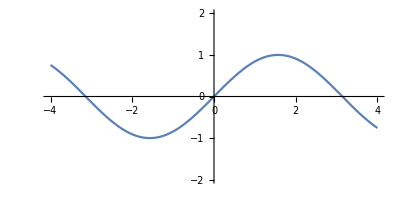

```mathematica
Plot[f[x], {x, -4, 4}, PlotRange -> {-2,2}, AspectRatio -> Automatic]
```

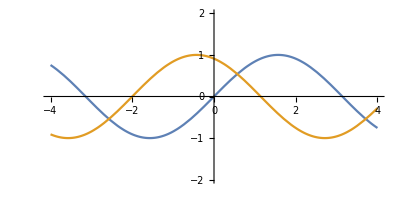

```mathematica
Plot[{f[x],f[x+2]}, {x, -4, 4}, PlotRange -> {-2,2}, AspectRatio -> Automatic]
```

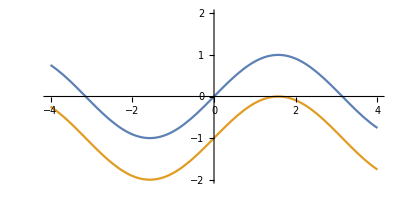

```mathematica
Plot[{f[x],f[x]-1}, {x, -4, 4}, PlotRange -> {-2,2}, AspectRatio -> Automatic]
```

Replacing x with x+2 shifts the graph to the left in this case. Replacing the f(x) with f(x)-1 shifts the graph down.

```mathematica
Clear[f]
f[x_] := x^2-x^3
```

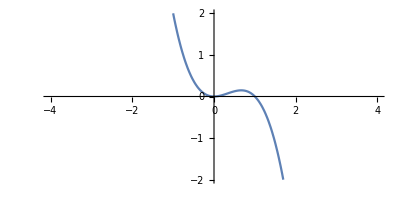

```mathematica
Plot[f[x], {x, -4, 4}, PlotRange -> {-2,2}, AspectRatio -> Automatic]
```

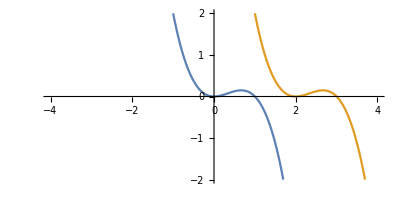

```mathematica
Plot[{f[x],f[x-2]}, {x, -4, 4}, PlotRange -> {-2,2}, AspectRatio -> Automatic]
```

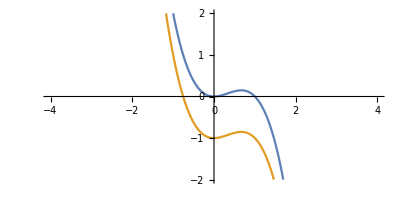

```mathematica
Plot[{f[x],f[x]-1}, {x, -4, 4}, PlotRange -> {-2,2}, AspectRatio -> Automatic]
```

```mathematica
Replacing x with x-2  shifts the graph to the right in this case. Replacing the f(x) with f(x)-1 shifts the graph down
```

## Experiment 2.3

For the functions y=f(x) below, examine the effect of replacing x by c x for the different values of c given:

	1.  f(x)=x(x^2-1),  c=2, c=-2.
	
	2.  f(x)= cos(x+1), c=3, c=1/2.
	
	3. f(x)=|x|, c=3, c=1/2.
	
	Explain the effect replacing  2x by 2 x+a has on the function f(x), for different values of a given:
	
	4.  f(x)=sin(2 x),  a=-1, a=π/2.

Your answer should include a concise statement as to the effect each of these operations has.

```mathematica
Clear[f]
f[x_]:=Cos[x+1]
```

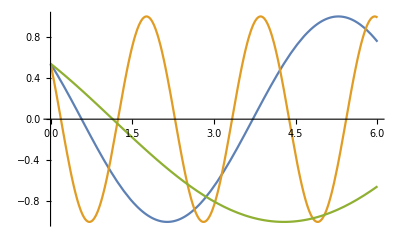

```mathematica
Plot[{f[x], f[3x], f[1/2x]}, {x, 0, 6}]
```

This operation made the function biggger with more zeroes and also smaller with less zeroes. The 3x made it larger and more frequent and the 1/2x made it smaller and less frequent

## Experiment 2.4

Test the following functions for symmetry with respect to the y-axis and the origin.

     	1.  f(x)=(sin x)/x,     2.  f(x)=(sin(x)+ x^3)/(x^2 + 1),    3.  f(x)=(e^x + 1)/x,    4.  f(x)=x cos(x^3 + x).
     	
     	5.  f(x)=(cos x)/x,    6.  f(x)=(cos(x)+ x^3)/(x^2 + 1),   7.  f(x)=(e^x+e^-x)/x.
     	
     	In each case explain what type of symmetry is involved (if any).

```mathematica
Clear[f,x]
f[x_]:= Sin[x]/x
```

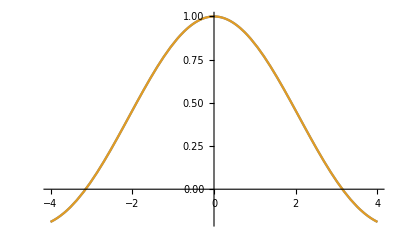

```mathematica
Plot[{f[x],f[-x]},{x,-4,4}]
```

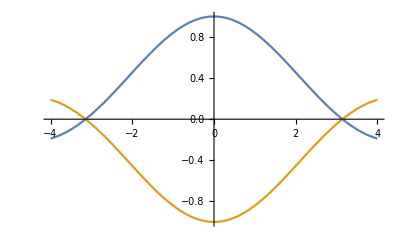

```mathematica
Plot[{f[x],-f[-x]},{x,-4,4}]
```

The function is symmetric with respect to the y-axis but not symmetric with respect to the origin.

```mathematica
Clear[f,x]
f[x_]:= (Sin[x]+x^3)/(x^2+1)
```

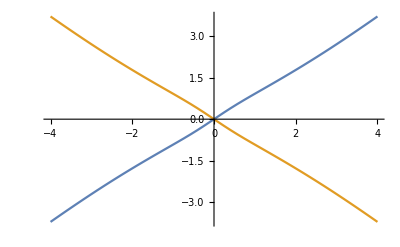

```mathematica
Plot[{f[x],f[-x]},{x,-4,4}]
```

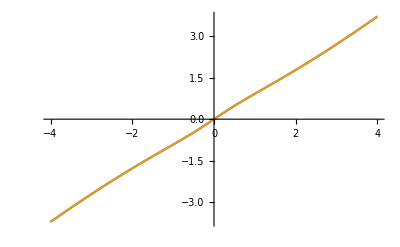

```mathematica
Plot[{f[x],-f[-x]},{x,-4,4}]
```

The function is not symmetric with respect to the y-axis but is symmetric with respect to the origin

```mathematica
Clear[f,x]
f[x_]:= (E^x+1)/(x)
```

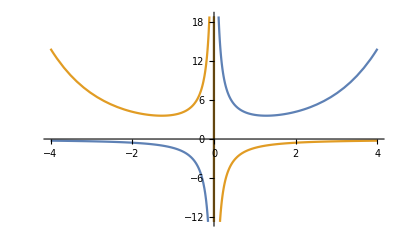

```mathematica
Plot[{f[x],f[-x]},{x,-4,4}]
```

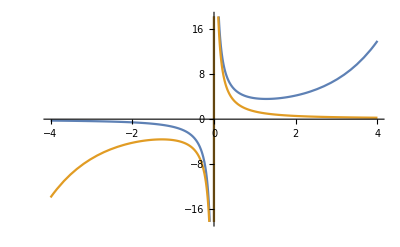

```mathematica
Plot[{f[x],-f[-x]},{x,-4,4}]
```

The function is not symmetric with respect to the y-axis and is not symmetric with respect to the origin

```mathematica
Clear[f,x]
f[x_]:= (Cos[x]+x^3)/(x^2+1)
```

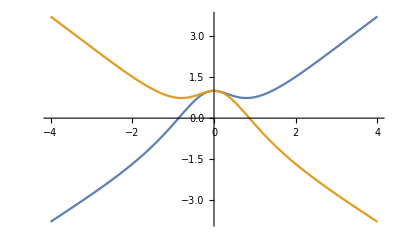

```mathematica
Plot[{f[x],f[-x]},{x,-4,4}]
```

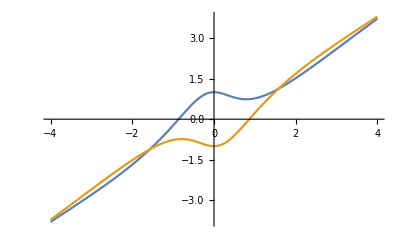

```mathematica
Plot[{f[x],-f[-x]},{x,-4,4}]
```

The function is not symmetric with respect to the y-axis or the origin.